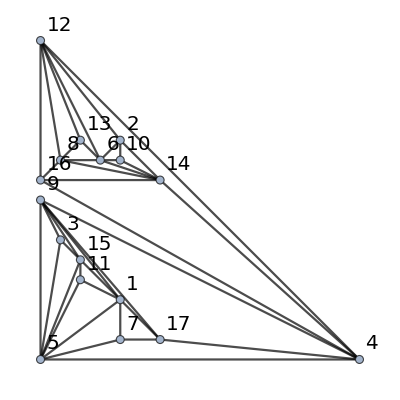

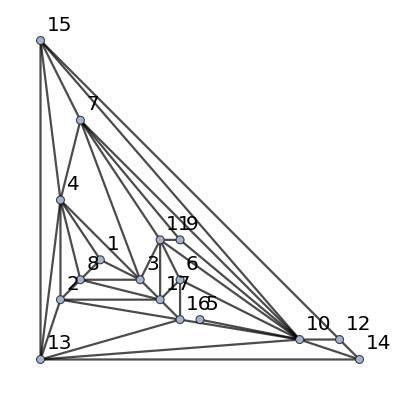

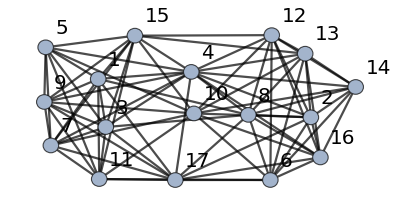

```mathematica
G1=System`Graph[{1<->5,1<->7,1<->9,1<->11,1<->15,1<->17,2<->6,2<->10,2<->12,2<->14,3<->5,3<->9,3<->15,4<->5,4<->9,4<->12,4<->14,4<->16,4<->17,5<->7,5<->9,5<->11,5<->15,6<->8,6<->10,6<->12,6<->13,6<->14,7<->17,8<->12,8<->13,8<->14,8<->16,9<->15,9<->17,10<->14,11<->15,12<->13,12<->16,14<->16},GraphLayout->"PlanarEmbedding",VertexLabels->"Name",VertexSize->0.4,VertexLabelStyle->Directive[Black,20],EdgeStyle->{{Thickness[0.004],Black}}]
G2=System`Graph[{1<->3,1<->4,1<->8,2<->4,2<->8,2<->13,2<->16,2<->17,3<->4,3<->7,3<->8,3<->11,3<->17,4<->7,4<->8,4<->13,4<->15,5<->10,6<->10,6<->11,6<->16,6<->17,7<->9,7<->10,7<->11,7<->15,8<->17,9<->10,9<->11,10<->11,10<->12,10<->13,10<->14,10<->15,10<->16,11<->17,12<->14,12<->15,13<->14,13<->15,13<->16,16<->17},GraphLayout->"PlanarEmbedding",VertexLabels->"Name",VertexSize->0.4,VertexLabelStyle->Directive[Black,20],EdgeStyle->{{Thickness[0.004],Black}}]
GUNION=GraphUnion[G1,G2,VertexLabels->"Name",VertexSize->0.4,VertexLabelStyle->Directive[Black,20],EdgeStyle->{{Thickness[0.004],Black}}]
GUNIONComplement=GraphComplement[GUNION,VertexLabels->"Name",VertexSize->0.1,VertexLabelStyle->Directive[Black,20],EdgeStyle->{{Thickness[0.004],Black}}];
```

```mathematica
<<Combinatorica`
<<GraphUtilities`
BrelazColoringList[G_]:=(brelazz=BrelazColoring@ToCombinatoricaGraph[G];Print[Table[{i,Part[brelazz,i]},{i,Length[brelazz]}]//TableForm];Return[brelazz]);
BrelazChromatic[G_]:=Max[BrelazColoring@ToCombinatoricaGraph[G]];
MVCColoringList[G_]:=(mvc=MinimumVertexColoring@ToCombinatoricaGraph[G];Print[Table[{i,Part[mvc,i]},{i,Length[mvc]}]//TableForm];Return[mvc]);
GetChromaticNumber[G_]:=Return[Max[MinimumVertexColoring@ToCombinatoricaGraph[G]]];
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
GUNIONCR=Ceiling[VertexCount[GUNION]/2];
GPruned=GUNION;
i=1;
Parallelize[While[i≤ VertexCount[GUNION],If[GetChromaticNumber[VertexDelete[GPruned,i]]≥ GUNIONCR,GPruned=VertexDelete[GPruned,i];Print[i,": DELETED " ],Print[i]];i++];]
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

```mathematica
GUNIONEdgeList=EdgeList[GPruned];
GUNIONEdgeListCnt=EdgeCount[GPruned];
i=1;
Parallelize[While[i≤ GUNIONEdgeListCnt,If[GetChromaticNumber[EdgeDelete[GPruned,GUNIONEdgeList[[i]]]]≥ GUNIONCR,GPruned=EdgeDelete[GPruned,GUNIONEdgeList[[i]]];Print[GUNIONEdgeList[[i]],": DELETED " ],Print[GUNIONEdgeList[[i]]]];i++];]
```

1<->2

1<->3

1<->4

1<->6

1<->8

1<->11

1<->12

1<->14

1<->15

1<->17

2<->3

2<->4

2<->6

$Aborted

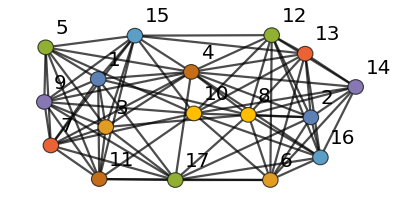

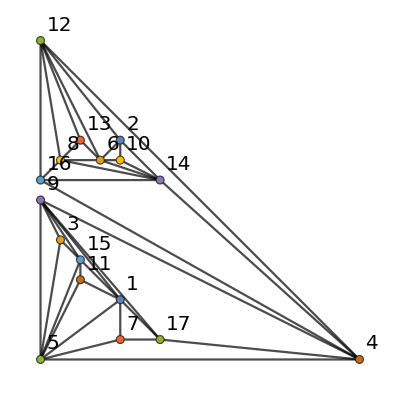

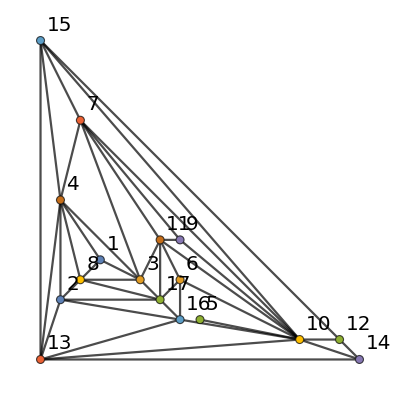

```mathematica
mvc={1,1,2,6,3,2,4,8,5,8,6,3,4,5,7,7,3};
GUNIONCOLORED=SetProperty[GUNION,System`VertexStyle->Thread[System`VertexList[GUNION]->(ColorData[97]/@mvc)]]
G1=SetProperty[G1,System`VertexStyle->Thread[System`VertexList[GUNION]->(ColorData[97]/@mvc)]]
G2=SetProperty[G2,System`VertexStyle->Thread[System`VertexList[GUNION]->(ColorData[97]/@mvc)]]
Export["1.eps",G1];
Export["2.eps",G2];
```

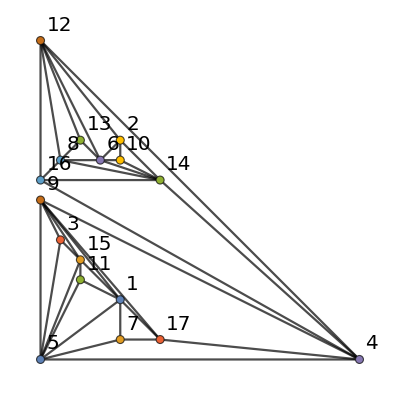

```mathematica
G1=System`Graph[{1<->5,1<->7,1<->9,1<->11,1<->15,1<->17,2<->6,2<->10,2<->12,2<->14,3<->5,3<->9,3<->15,4<->5,4<->9,4<->12,4<->14,4<->16,4<->17,5<->7,5<->9,5<->11,5<->15,6<->8,6<->10,6<->12,6<->13,6<->14,7<->17,8<->12,8<->13,8<->14,8<->16,9<->15,9<->17,10<->14,11<->15,12<->13,12<->16,14<->16},GraphLayout->"PlanarEmbedding",VertexLabels->"Name",System`VertexStyle->Thread[System`VertexList[G1]->(ColorData[97]/@{1,1,2,6,3,2,4,8,5,8,6,3,4,5,7,7,3})],VertexSize->0.4,VertexLabelStyle->Directive[Black,20],EdgeStyle->{{Thickness[0.004],Black}}]
```